Remove::rmnsm: There are no symbols matching ""Global`*"".

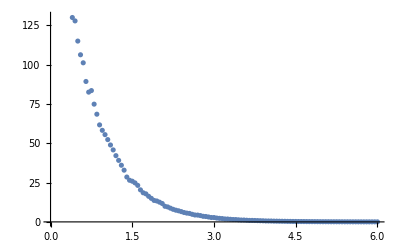

{a→251.707,b→1.52874}

{c→3.27067×10^-11}

```mathematica
Remove["Global`*"]
data=Import["/Users/Felix/GitHub/Envariabel-projekt/matserie.dat"];
ListPlot[data]
FindFit[data, a ⅇ^(- b x), {a,b}, x]
FindFit[data,251.70653701301623 ⅇ^(-t/(20000000000 c)) , c,t]
data[[All,2]];
```

```mathematica
Remove["Global`*"]
R=20*10^9;
DSolve[{u'[t]+u[t]*1/(R*c)==0}, u[t], t]
```

{{u[t]→ⅇ^(-t/(20000000000 c)) C[1]}}

```mathematica
Remove["Global`*"]
R=20*10^9;
C0=3.27*10^-11;


D[251.707*ⅇ^(-t/(R*C0))]*C0
```

8.23082×10^-9 ⅇ^(-1.52905 t)

```mathematica
Remove["Global`*"]
c=3.270666888845813*^-11;
Solve[u==251.70653701301623 ⅇ^(-t/(20000000000 (c/2))) ,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-0.327067 Log[0.00397288 u]}}

```mathematica
Remove["Global`*"]
```

```mathematica
i[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
i[0]
Solve[4.11540945*^-9==8.2308189*^-9 ⅇ^(-1.529051987767584t),t]
```

8.23082×10^-9

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.453318}}

```mathematica
(8.2308189*^-9)/2
```

4.11541×10^-9

```mathematica
Remove["Global`*"]
q[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
q[0];
Solve[q[0]/2==q[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.453318}}

```mathematica
Remove["Global`*"]
c=3.270666888845813*^-11;
i[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
u[t_]=251.70653701301623 ⅇ^(-t/(20000000000 c)) ;
p[t_]=u[t]*i[t];
En[t_]=p[t]*t;
Limit[p[t],t->Infinity]
Limit[Integrate[En[t],{t,0,R}], R->Infinity]
```

0.

2.21575×10^-7

```mathematica
Remove["Global`*"]
c0=3.270666888845813*^-11;
c=c0*1.1
DSolve[{R* q'[t]+q[t]/c==250,q[0]==c0*250},q[t],t]
FullSimplify[%]
```

3.59773×10^-11

{{q[t]→8.99433×10^-9 ⅇ^(-(2.77953×10^10 t)/R) (-0.0909091+1. ⅇ^((2.77953×10^10 t)/R))}}

{{q[t]→8.99433×10^-9-8.17667×10^-10 ⅇ^(-(2.77953×10^10 t)/R)}}

```mathematica
Remove["Global`*"]
q[t_]=8.994333944325988*^-9 ⅇ^(-(2.7795276620534058*^10 t)/R) (-0.09090909090909122+1. ⅇ^((2.7795276620534058*^10 t)/R));
i[t_]=D[q[t],t];
FullSimplify[%]
i[250*10^-6];
FullSimplify[%]
i[0];
FullSimplify[%];
```

(22.7273 ⅇ^(-(2.77953×10^10 t)/R))/R

(22.7273 ⅇ^(-6.94882×10^6/R))/R

```mathematica
Solve[(22.72727272727281 ⅇ^(-6.948819155133515*^6/R))/R==1*10^-6,R]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→3.99964×10^6},{R→1.3671×10^7}}

```mathematica
Remove["Global`*"]
c0=3.270666888845813*^-11;
DSolve[{R* q'[t]+q[t]/c==250,q[0]==c0*250},q[t],t];
FullSimplify[%];
q[t_]=250. c+(8.176667222114532*^-9-250. c) ⅇ^(-t/(c R));
i[t_]=D[q[t],t];
R = 3.999639258464372*^6;
i[250*10^-6];
(*Solve[-(2.5002254837951104*10^-7  *(8.176667222114532*10^-9 -250* c) ⅇ^(-6.250563709487777*^-11/c))/c==1*10^-6, c]*)
Expand[%]
```

0.0000625056 ⅇ^(-6.25056×10^-11/c)-(2.04435×10^-15 ⅇ^(-6.25056×10^-11/c))/c

```mathematica
Remove["Global`*"]
D[251.70653701301623 ⅇ^(-t/(r*c)) ,t]
```

-(251.707 ⅇ^(-t/(c r)))/(c r)

```mathematica
Remove["Global`*"]
r=6.765*10^6;
t=250*10^6;
Solve[-(251.70653701301623 ⅇ^(-t/(c *r)))/(c r)==(22.72727272727281 ⅇ^(-t/(r*c)))/r,c]
```

{{c→-11.0751}}

```mathematica
Remove["Global`*"]
r=6.765*10^6
t=250*10^-6;
u[t_]=251.70653701301623 ⅇ^(-t/(r*c)) ;
q[t_]=-22.72727272727281 c ⅇ^(-t/(c*r));
Solve[q[t]/u[t]==c, c]
```

6.765×10^6

{{c→0.}}

```mathematica
Remove["Global`*"]
q[t_]=250. Subscript[c, 0]+(8.176667222114532*^-9-250. Subscript[c, 0]) ⅇ^(-t/(c* r));
Subscript[c, 0]=3.270666888845813*^-11;
r=6.765*10^6;
t=250*10^-6;
Solve[(p*q[0]*ⅇ^(-t/(r*Subscript[c, 0])))/(r*Subscript[c, 0])==1*10^-6,p]
```

{{p→0.0837592}}

{{u→377.914}}